```mathematica
Quit
```

```mathematica
llbdev2
```

Lazy Loading on

PacletInstall::newervers: A paclet named UnitTable with a newer version number (13.0.0) is already installed. If you wish to install an older version, use PacletUninstall to remove the existing version first, or call PacletInstall with IgnoreVersion->True.

Loaded SLL`Dev2 in 157 seconds, at Thu 14 Apr 2022 05:48:53

Your session is not against the production Object Store, but is using https://constellation-stage.emeraldcloudlab.com

### Code

#### ExperimentFake

```mathematica
(*
	TODO 
	- put this in codebase
*)
ClearAll[ExperimentFake];
DefineOptions[ExperimentFake,
Options:>{
	{
		OptionName->Parameter1,
		Default->4,
		AllowNull->False,
		Description->"A descriptor.",
		Widget->Widget[Type->Number,Pattern:>GreaterP[0]],
		Category->"General Information"
	},
	{
		OptionName->Parameter2,
		Default->2,
		AllowNull->False,
		Description->"Another descriptor.",
		Widget->Widget[Type->Enumeration,Pattern:>Alternatives@@Range[0,4]],
		Category->"General Information"
	},
	{
		OptionName->Parameter3,
		Default->5,
		AllowNull->False,
		Description->"Another descriptor 3.",
		Widget->Widget[Type->Number,Pattern:>GreaterP[0]],
		Category->"General Information"
	}
}]
ExperimentFake[samples_, myOps:OptionsPattern[]]:=Module[
{safeOps, p1, p2, xy, chromData, prot},
	safeOps = SafeOptions[ExperimentFake,ToList[myOps]];
	{p1,p2} = Lookup[safeOps, {Parameter1,Parameter2}];
	
	xy = QuantityArray[With[{b= 10-(p1-7)^2,a=(p2-2)^2}, 
		N@Table[{x,a+b*Exp[-(x-5+a)^2]},{x,0,10,.3}]
	],{Minute,AbsorbanceUnit}];

	chromData = Upload[<|Type->Object[Data,Chromatography],Absorbance->xy|>];

	prot = Upload[<|
		Type->Object[Protocol],
		Status->Null,
		Append[Data]->{Link[chromData,Protocol]},
		ResolvedOptions->safeOps
	|>];
	
	prot

]
```

#### Objective Functions

```mathematica
MaxDataHeight[prot:ObjectP[Object[Protocol]]]:=MaxDataHeight[First[Download[prot,Data]]];
MaxDataHeight[data:ObjectP[Object[Data,Chromatography]]]:=Module[{},

	Max[Download[data,Absorbance][[;;,2]]]

];


MaxPeakHeight[prot:ObjectP[Object[Protocol]]]:=MaxPeakHeight[First[Download[prot,Data]]];
MaxPeakHeight[data:ObjectP[Object[Data,Chromatography]]]:=Module[{pkObj},

	pkObj = AnalyzePeaks[data];

	Max[Download[pkObj,Height]]

];
```

#### DOE

```mathematica
(*
	TODO 
	- EXPORT 'Variable' in manifest
*)
Variable=DesignOfExperiment`Private`Variable; (* remove when this gets exported *)
ClearAll[DOE];
Options[DOE] = {
	ObjectiveFunction -> MaxDataHeight 
};
SetAttributes[DOE,HoldFirst];
DOE[myExperiment_[myExpParameters___],ops:OptionsPattern[]]:=Module[{scriptPacket,doeScript,anaObj,calls,
	expFunc,samples,variableOptions,fixedOptions,allOps,varOpNames},
	
	(*
		Parse the input call and generate the set of Variables
	*)
	{expFunc,samples,variableOptions,fixedOptions} = DesignOfExperiment`Private`resolveDesignOfExperimentInputs[myExperiment[myExpParameters]];
	varOpNames = Keys[variableOptions];

	allOps=DesignOfExperiment`Private`gridGeneration[expFunc,variableOptions,fixedOptions,Method->GridSearch];

	(*
		Initialize the analysis objet
		TODO: fill in any other fields we know at this point
	*)
	anaObj=Upload[<|Type->Object[Analysis,DesignOfExperiment],
		ObjectiveFunction->AreaOfTallestPeak,
		Replace[ParameterSpace]->varOpNames
	|>];
	
	(* 
		upload this b/c I need the object ID
	*)
	doeScript = Upload[<|
		Type->Object[Notebook,Script,DesignOfExperiment],
		Replace[Parameters]->varOpNames,
		Replace[Ranges]->Transpose[Lookup[allOps,varOpNames]],
		Replace[DesignOfExperimentAnalyses]->Link[anaObj,Reference]
	|>];	
	
	
	(*
		Make a script riffling the experiment calls with analysis calls and updateThingy calls
		Need the analysis object at this point because it's an argument to the AnalyzeDOE calls
	*)
	scriptExpr= generateScriptCalls[samples,allOps,doeScript,anaObj,varOpNames];
		
	(* 
		Call ExperimentScriptDOE
	*)
	scriptPacket = First@With[{scriptExpr=scriptExpr},
		ExperimentScript@@Append[scriptExpr,Upload->False]
	];
	
	doeScript = Upload[Join[
		KeyDrop[scriptPacket,{Object,Type}],
		<|
			Object->doeScript			
		|>
	]];
	
	
	{doeScript, anaObj}
	
];
```

#### generateScriptCalls

```mathematica
ClearAll[generateScriptCalls];
generateScriptCalls[samples_,allOps_,doeID_,anaObj_,varOpNames_]:=Module[{calls},
	calls = Join@@Map[
		With[
			{
				prot=Unique["prot"],
				pSample = Lookup[#,varOpNames],
				opsSeq = Sequence@@#
			},
			Hold[
				experimentWrapper[
					prot=ExperimentFake[samples,opsSeq],
					updateScriptProtocolRunning[doeID,prot]
				],
				updateDOEStatusCompleted[doeID,prot],
				AnalyzeDOE[anaObj,prot,pSample]
			]
		]&,
		allOps
	];
	With[{calls=calls},
		With[{expr=With[{hcalls=Hold[calls]},CompoundExpression@@@hcalls]},Append[expr,Upload->False]]
	]
]
```

#### update functions

```mathematica
ClearAll[updateScriptProtocolRunning];
updateScriptProtocolRunning[doeScript_,prot_]:=Module[{},
	Upload[<|Object->doeScript,Append[RunningProtocols]->Link[prot]|>]
];

ClearAll[updateDOEStatusCompleted];
updateDOEStatusCompleted[doeScript_,prot_]:=Module[{},
	Upload[<|Object->doeScript,
		Replace[RunningProtocols]->DeleteCases[doeScript[RunningProtocols],prot|Link[prot,___]],
		Append[CompletedProtocols]->Link[prot]
	|>]
];
```

#### AnalyzeDOE

```mathematica
(*
	TODO 
	- make sure all analysis fields are filled in
	- update to use real objective function from option
	- pull pSample from prot (make a helper func for this because it happens in several of these DOE functions)
	- pull anaObj from prot, so only prot is input?
*)
ClearAll[AnalyzeDOE];
AnalyzeDOE[anaObj_,prot_,pSample_]:=Module[{score,objf},
	(*objf = Download[anaObj,ObjectiveFunction];*)
	objf = MaxDataHeight;
	
	score = objf[prot];

	(*
		TODO - update any other fields in here
	*)
	Upload[<|Object->anaObj,
		Append[ExperimentParameters]->{pSample},
		Append[Data]->Link[First[Download[prot,Data]]],
		Append[ObjectiveValues] -> score		
	|>];
	
	updateBestPoints[anaObj];
	
	anaObj
];


(*
	TODO - Also have some handling for errors/edges, like multiple extrema
	Define interface so users can provide their own function
*)
updateBestPoints[anaObj_]:=Module[{objVals,parVals,order, bestInd},

	{objVals,parVals} = Download[anaObj,{ObjectiveValues,ExperimentParameters}];

	order = Ordering[objVals];
	
	bestInd = order[[-1]];
	
	Upload[<|Object->anaObj,
		OptimalObjectiveValue->objVals[[bestInd]],
		Replace[OptimalParameters]->{parVals[[bestInd]]}
	|>]
	
];
```

#### areWeDone

```mathematica
(*
	This should check, depending on options:
		* have we visited all of the points
		* have we converged to an extrema 
		* have we hit max number of experiments
*)
areWeDone[anaObj_]:= Something;
```

#### RunScriptDOE

```mathematica
(*
	TODO
	- make RunScriptDOE a real function
	- figure out termination condition. which field in the script tells us it's finished?
	- for now, add option like Fake->True which triggers this version
	- what does Fake->False do?  just RunScript?
*)
ClearAll[RunScriptScriptDOE];
RunScriptScriptDOE[script_]:=Module[{keepGoing=True,colors,pranges,varOpNames},
	{varOpNames,pranges} = Download[script,{Parameters,Ranges}];
	Print[Dynamic[Grid[Partition[Map[Item[#,Background->colors[#]]&,Transpose[pranges]],Length[Union[Last[pranges]]]],Frame->All],TrackedSymbols->{colors}]];
	colors[_]:=Yellow;
	Catch[While[keepGoing,
		Module[{currentProts,completedProts,resolvedProtOps,currentValues},
			completedProts = Download[script,CompletedProtocols];
			resolvedProtOps = Download[completedProts,ResolvedOptions];
			currentValues = Lookup[resolvedProtOps,varOpNames];
			Map[(colors[#] = Green)&,currentValues];
				
			(* 
				re-start script evaluation
				it will run until it generates a protocol
			 *)
			Check[
				RunScript[script];,
				(
					keepGoing=False;
					Throw[script,"ScriptDone"];
				),
				{Error::ScriptAlreadyCompleted}
			];
		
			(* 
				update the current protocol status to completed
				now, next time we RunScript it will continue to the next step
			*)
			currentProts = Download[script,CurrentProtocols[Object]];
			Upload[Map[<|Object->#,Status->Completed|>&,currentProts]];
			
		]		
	],"ScriptDone"]
	
];
```

#### PlotDOE

```mathematica
(*
	TODO
	- make this  a real function
	- 
*)
ClearAll[PlotDOE];
PlotDOE[anaObj_]:=Module[{xx,y,xxbest,ybest},

	{xx,y,xxbest,ybest} = Download[anaObj,{ExperimentParameters,ObjectiveValues,OptimalParameters,OptimalObjectiveValue}];
	
	If[Length[xx[[1]]]===2,
		Show[
			ListContourPlot[Transpose[Append[Transpose[xx],y]]],
			ListPlot[{xxbest},PlotStyle->List[Red,PointSize[2]]]
		],
		Show[
			ListPlot[Transpose[{xx,y}], PlotMarkers->Automatic,Joined->True],
			ListPlot[{{xxbest[[1]],ybest}},PlotStyle->List[Red,PointSize[.02]]]
		]
	]

]
```

### Running it

```mathematica
{script,anaObj} = DOE[
ExperimentFake[mySamples,Parameter1->Variable[{4,5,6,7}],Parameter2->Variable[{1,2,3}],Parameter3->5]
]
```

-Graphics-New objects added to Constellation:{Object[Analysis,DesignOfExperiment,id:6V0npvmDNRvZ],Object[Notebook,«2»,i…vX]}

{Object[Notebook,Script,DesignOfExperiment,id:9RdZXv1JaAvX],Object[Analysis,DesignOfExperiment,id:6V0npvmDNRvZ]}

```mathematica
RunScriptScriptDOE[script]
```

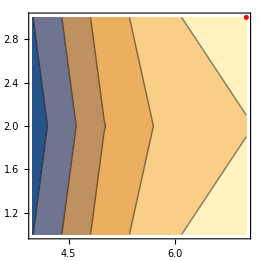

```mathematica
PlotDOE[anaObj]
```

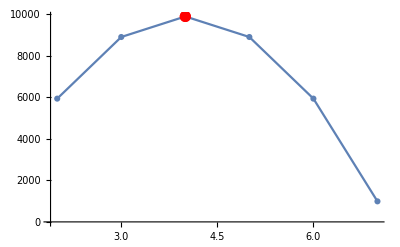

```mathematica
PlotDOE[Object[Analysis,DesignOfExperiment,"id:GmzlKjPZr5Pk"]]
```

```mathematica
Inspect[anaObj]
```

## Issues

### Scripts

#### Need to parallelize the calls for grid-search case, or do them all in one call

#### How will the script update itself if using an iterative (non-grid-search) method?

Can’t pre-write the steps if we don’t know them.  It will need to append new cells to itself for each new step

##### Do we want each script to make a new script, so each script is just one step?

## old scratch

### Data generation

```mathematica
Plot3D[Exp[-(x-5)^2],{x,0,10},{p1,3,7},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[With[{b=10-(p1-4)^2},b*Exp[-(x-5)^2]],{x,0,10},{p1,1,7},PlotRange->All]
```

-Graphics3D-

```mathematica
?ContourPlot
```

```mathematica
With[{b=10-(p1-4)^2, a=Tanh[p2]},a+b*Exp[-(x-5)^2]]/.p1->3/.p2->1
```

9 ⅇ^(-(-5+x)^2)+Tanh[1]

```mathematica
c
```

c

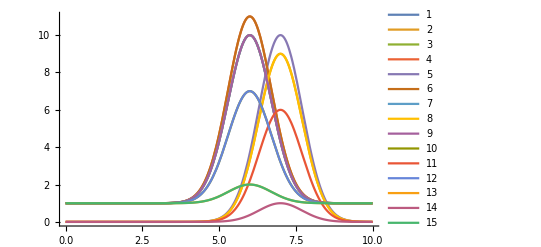

```mathematica
With[{f=Flatten[Table[With[{b=10-(p1-4)^2, a=(p2-2)^2},a+b*Exp[-(x-7+a)^2]],{p1,3,7,1},{p2,1,3,1}]]},
Plot[f,{x,0,10},PlotRange->All,PlotLegends->Automatic]
]
```

```mathematica
ContourPlot[With[{b=10-(p1-4)^2, a=Tanh[p2]},a+b*Exp[-(x-5)^2]],{p1,2,7},{p2,-1,1}]
```

-Graphics-

```mathematica
With[{p1=4},Plot3D[With[{b=10-(p1-4)^2, a=Tanh[p2]},b*Exp[-(x-5)^2]],{x,0,10},{p2,1,7},PlotRange->All]]
```

-Graphics3D-

```mathematica
makeData[p1_]:=With[{b= 10-(p1-4)^2}, 
N@Table[{x,b*Exp[-(x-5)^2]},{x,0,10,.3}]
]
```

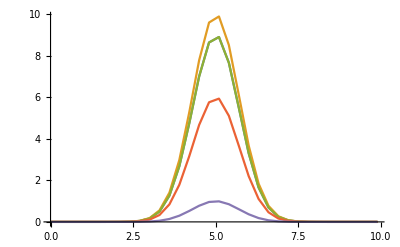

```mathematica
ListLinePlot[makeData/@Range[3,7],PlotRange->All]
```

```mathematica
chromDatas = Upload@Map[
<|Type->Object[Data,Chromatography],Absorbance->QuantityArray[makeData[#],{Minute,AbsorbanceUnit}]|>&,
Range[3,7]
]
```

-Graphics-New objects added to Constellation:{Object[Data,Chromatography,id:01G6nvwLpwvY],«3»,Object[Data,«14»,id:WNa4ZjKEGKj8]}

{Object[Data,Chromatography,id:M8n3rx0XZ0x5],Object[Data,Chromatography,id:WNa4ZjKEGKj8],Object[Data,Chromatography,id:54n6evL3RLvq],Object[Data,Chromatography,id:n0k9mG8dw8Gr],Object[Data,Chromatography,id:01G6nvwLpwvY]}

```mathematica
prot = Upload[<|Type->Object[Protocol],Append[Data]->Map[Link[#,Protocol]&,chromDatas]|>]
```

-Graphics-New objects added to Constellation:{Object[Protocol,id:eGakldJ76Jd1]}

Object[Protocol,id:eGakldJ76Jd1]

```mathematica
ExperimentFake[{cat,dog}]
```

-Graphics-New objects added to Constellation:{Object[Protocol,id:vXl9j57Owa8Z],Object[Data,Chromatography,id:N80DNj1qdEpk]}

Object[Protocol,id:vXl9j57Owa8Z]

```mathematica
ExperimentFake[{cat,dog},Parameter1->3]
```

-Graphics-New objects added to Constellation:{Object[Protocol,id:Z1lqpMzjELZz],Object[Data,Chromatography,id:1ZA60vLjoK1w]}

Object[Protocol,id:Z1lqpMzjELZz]

### Script

```mathematica
testScript=ExperimentScript[
ExperimentFake[{dog},Parameter1-> 4];
ExperimentFake[{cat},Parameter1-> 5];
]
```

-Graphics-New objects added to Constellation:{Object[Notebook,Script,id:N80DNj1qdw0D]}

Object[Notebook,Script,id:N80DNj1qdw0D]

```mathematica
Object[Protocol,"id:54n6evL3RooN"][Status]
```

Completed

```mathematica
RunScript[testScript]
```

-Graphics-New objects added to Constellation:{-Graphics- | 84b6e517-1d68-4359-9ce9-aaed23028361.txt |  | 
 |  | 
 |  | ,-Graphics- | 84b6e517-1d68-4359-9ce9-aaed23028361.txt |  | 
 |  | 
 |  | ,-Graphics- | 9268e741-7a16-4589-b8d8-364499436daf.txt |  | 
 |  | 
 |  | }

Object[Notebook,Script,id:N80DNj1qdw0D]

```mathematica
%//Inspect
```

```mathematica
testScript=ExperimentScript[
ExperimentFake[{dog},Parameter1-> 4];
ExperimentFake[{cat},Parameter1-> 5];
]
```

-Graphics-New objects added to Constellation:{Object[Notebook,Script,id:jLq9jXvnPkE6]}

Object[Notebook,Script,id:jLq9jXvnPkE6]

```mathematica
Inspect[testScript]
```

```mathematica
RunScript[testScript]
```

Global`f$::shdw: Symbol f$ appears in multiple contexts {Global`,ECL`}; definitions in context Global` may shadow or be shadowed by other definitions.

-Graphics-New objects added to Constellation:{-Graphics- | 14701a55-3403-4b19-a9a3-6747ede8a2f6.txt |  | 
 |  | 
 |  | ,-Graphics- | 14701a55-3403-4b19-a9a3-6747ede8a2f6.txt |  | 
 |  | 
 |  | ,-Graphics- | 6a3967a9-0766-47dd-bfcb-79b7e9cd1eb4.txt |  | 
 |  | 
 |  | }

Object[Notebook,Script,id:jLq9jXvnPkE6]

```mathematica
currentProts = Download[testScript,CurrentProtocols[Object]]
```

{Object[Protocol,id:E8zoYvN09lRa]}

```mathematica
Download[currentProts,Status]
```

{Processing}

```mathematica
Upload[Map[<|Object->#,Status->Completed|>&,currentProts]]
```

{Object[Protocol,id:E8zoYvN09lRa]}

```mathematica
Download[testScript,CurrentProtocols[Object]]
```

{Object[Protocol,id:E8zoYvN09lRa]}

```mathematica
RunScript[testScript]
```

-Graphics-New objects added to Constellation:{-Graphics- | dc6ecc08-c104-456a-a489-ee92b682d52c.txt |  | 
 |  | 
 |  | ,-Graphics- | dc6ecc08-c104-456a-a489-ee92b682d52c.txt |  | 
 |  | 
 |  | ,-Graphics- | db7fc50b-aa1a-4dd2-a16b-fc3580d317eb.txt |  | 
 |  | 
 |  | }

Object[Notebook,Script,id:jLq9jXvnPkE6]

```mathematica
Inspect[testScript]
```

```mathematica
ClearAll[RunScriptScriptDOE];
RunScriptScriptDOE[script_,testCalls_]:=With[{heldCalls=First[List@@@Map[Hold,testCalls,{2}]]},

	(* just using testCalls to easily get the number of steps and print the calls running.  *)
	Print[heldCalls];
	Table[
		Module[{currentProts},
			(* evaluate a line *)
			RunScript[script];
			Print["Evaluating :",heldCalls[[n]]];
			Pause[2];
			currentProts = Download[script,CurrentProtocols[Object]];
	
			(* update the current protocol status to completed *)
			Upload[Map[<|Object->#,Status->Completed|>&,currentProts]];
			Pause[2];
			Print["Done running ",heldCalls[[n]]];			
			
		],
		
		{n,1,Length[heldCalls]-1}
		
	]
	
];
```

```mathematica
testCalls=Hold[
ExperimentFake[{dog},Parameter1-> 4];
ExperimentFake[{cat},Parameter1-> 5];
ExperimentFake[{cat},Parameter1-> 6];
];
```

```mathematica
testScript = ExperimentScript@@testCalls
```

-Graphics-New objects added to Constellation:{Object[Notebook,Script,id:aXRlGn6rvdOm]}

Object[Notebook,Script,id:aXRlGn6rvdOm]

```mathematica
RunScriptScriptDOE[testScript,testCalls]
```

{Hold[ExperimentFake[{dog},Parameter1→4]],Hold[ExperimentFake[{cat},Parameter1→5]],Hold[ExperimentFake[{cat},Parameter1→6]],Hold[Null]}

Evaluating :Hold[ExperimentFake[{dog},Parameter1→4]]

Done running Hold[ExperimentFake[{dog},Parameter1→4]]

Evaluating :Hold[ExperimentFake[{cat},Parameter1→5]]

Done running Hold[ExperimentFake[{cat},Parameter1→5]]

Evaluating :Hold[ExperimentFake[{cat},Parameter1→6]]

Done running Hold[ExperimentFake[{cat},Parameter1→6]]

-Graphics-New objects added to Constellation:{-Graphics- | a594e54a-600a-402f-b868-97b74f9d8ef3.txt |  | 
 |  | 
 |  | ,-Graphics- | 6356e593-fc8e-4dab-821e-33b77769f042.txt |  | 
 |  | 
 |  | ,-Graphics- | a594e54a-600a-402f-b868-97b74f9d8ef3.txt |  | 
 |  | 
 |  | ,-Graphics- | 55b8f998-6fdd-4f41-bc3d-fe200342387e.txt |  | 
 |  | 
 |  | ,-Graphics- | 004172db-88f9-4227-82af-2ff7eab444e9.txt |  | 
 |  | 
 |  | ,-Graphics- | 004172db-88f9-4227-82af-2ff7eab444e9.txt |  | 
 |  | 
 |  | ,-Graphics- | 6356e593-fc8e-4dab-821e-33b77769f042.txt |  | 
 |  | 
 |  | ,-Graphics- | 9be9d065-591b-494f-97a6-982e16a96b5a.txt |  | 
 |  | 
 |  | ,-Graphics- | bbaeaaaf-f146-488a-9fa8-f111a7a7fe79.txt |  | 
 |  | 
 |  | }

{Null,Null,Null}

### Plot